```mathematica
GeoPathPlot[x_]:=GeoGraphics[GeoPath[x],GeoRange->"World",Frame->True]
```

```mathematica
crossing=Import["/Users/robertmendelsohn/Desktop/Fathom5/crossing.csv"];
overtaking=Import["/Users/robertmendelsohn/Desktop/Fathom5/overtaking.csv"];
meeting=Import["/Users/robertmendelsohn/Desktop/Fathom5/meeting.csv"];
```

```mathematica
Flatten[crossing//DataProcessor,1]
```

{{47.9906,122.598},{47.9906,122.599},{47.9906,122.6},{0.,223.696},{47.9906,122.6},{47.9906,122.601},{47.9906,122.602},{47.9906,122.602},{47.9906,122.603},{47.9906,122.604},{47.9906,122.604},{47.9906,122.605},{47.9906,122.606},{47.9906,122.606},{47.9906,122.607},{47.9906,122.608},{47.9906,122.608},{47.9906,122.609},{47.9906,122.61},{47.9906,122.61},{47.9906,122.611},{47.9906,122.612},{47.9645,122.612},{47.965,122.612},{47.9654,122.613},{47.9658,122.613},{47.9662,122.614},{47.9667,122.614},{0.,223.696},{47.9671,122.615},{47.9675,122.615},{47.968,122.616},{47.9684,122.616},{47.9688,122.616},{47.9692,122.617},{47.9697,122.617},{47.9697,122.617},{47.9697,122.617},{47.9698,122.617},{47.97,122.618},{47.9701,122.618},{47.9703,122.618},{47.9704,122.618},{47.9706,122.618},{47.9707,122.618},{47.9709,122.618},{47.9711,122.618},{47.9712,122.619},{47.9714,122.619},{47.9715,122.619},{47.9717,122.619},{47.9719,122.619},{47.972,122.619},{47.9722,122.619},{47.9724,122.619},{47.9725,122.619},{47.9727,122.619},{47.9729,122.619},{47.973,122.619},{47.9732,122.619},{47.9734,122.62},{47.9736,122.62},{47.9737,122.62},{47.9739,122.62},{47.9741,122.62},{47.9743,122.62},{47.9744,122.62},{47.9746,122.62},{47.9748,122.62},{47.975,122.62},{47.9751,122.62},{47.9753,122.62},{47.9755,122.62},{47.9757,122.62},{47.9758,122.62},{47.976,122.62},{47.9762,122.62},{47.9764,122.62},{47.9765,122.62},{47.9767,122.62},{47.9769,122.62},{47.9771,122.619},{47.9772,122.619},{47.9774,122.619},{47.9776,122.619},{47.9777,122.619},{47.9779,122.619},{47.9781,122.619},{47.9783,122.619},{47.9784,122.619},{47.9786,122.619},{47.9788,122.619},{47.9789,122.619},{47.9791,122.619},{47.9792,122.618},{47.9794,122.618},{47.9796,122.618},{47.9797,122.618},{47.9799,122.618},{47.98,122.618},{47.9802,122.618},{47.9803,122.618}}

```mathematica
Flatten[overtaking//DataProcessor,1]
```

{{47.9685,122.611},{47.9688,122.612},{47.9692,122.612},{47.9696,122.612},{47.9699,122.613},{47.9703,122.613},{47.9707,122.614},{47.971,122.614},{47.9714,122.614},{47.9717,122.615},{47.9721,122.615},{0.,223.696},{47.9725,122.616},{47.9728,122.616},{47.9732,122.616},{47.9736,122.617},{47.9739,122.617},{47.9743,122.618},{47.9746,122.618},{47.959,122.606},{47.9595,122.607},{47.9599,122.607},{47.9604,122.608},{47.9608,122.608},{47.9613,122.609},{47.9617,122.609},{47.9622,122.61},{47.9626,122.61},{47.9631,122.611},{47.9635,122.611},{47.9639,122.612},{47.9644,122.612},{47.9648,122.612},{47.9653,122.613},{47.9657,122.613},{47.9662,122.614},{47.9666,122.614},{47.9671,122.615},{0.,223.696},{47.9675,122.615},{47.9679,122.616},{47.9684,122.616},{47.9688,122.617},{47.9693,122.617},{47.9697,122.618},{47.9702,122.618},{47.9707,122.619},{47.9711,122.619},{47.9716,122.62},{47.9721,122.62},{47.9721,122.62},{47.9725,122.621},{47.9727,122.621},{47.9729,122.621},{47.9731,122.621},{47.9732,122.621},{47.9734,122.622},{47.9736,122.622},{47.9738,122.622},{47.974,122.622},{47.9741,122.622}}

```mathematica
Flatten[meeting//DataProcessor,1]
```

{{47.9839,122.637},{47.9835,122.636},{47.9832,122.636},{47.9828,122.636},{47.9824,122.635},{47.9821,122.635},{47.9817,122.634},{47.9814,122.634},{47.981,122.633},{47.9807,122.633},{47.9803,122.633},{47.98,122.632},{47.9796,122.632},{47.9792,122.631},{47.9789,122.631},{47.9785,122.63},{47.9782,122.63},{47.9778,122.63},{47.9775,122.629},{47.9643,122.612},{47.9646,122.612},{47.9649,122.613},{47.9653,122.613},{47.9656,122.613},{47.9659,122.614},{47.9663,122.614},{47.9666,122.615},{47.967,122.615},{47.9674,122.616},{47.9677,122.616},{47.9681,122.616},{47.9684,122.617},{47.9688,122.617},{47.9692,122.618},{47.9695,122.618},{47.9699,122.618},{0.,223.696},{47.9702,122.619}}

```mathematica
Select[Select[Map[#[[-2;;-1]]&,crossing],Length[#]≥2&],NumberQ[#[[1]]]&]//Quiet//GeoPathPlot
```

-Graphics-

```mathematica
SecondarySorter[x_]:=SortBy[x,First]
```

```mathematica
DataProcessor3[x_]:=Map[#[[-2;;-1]]&,Map[SecondarySorter,SplitBy[SortBy[Map[{AbsoluteTime[#[[1]]],#[[2]],#[[-2]],#[[-1]]}&,Select[Select[Rest[x],(Length[#]≥7)&&(MemberQ[#,0]==False)&],StringLength[#[[1]]]≥8&]],#[[2]]&],#[[2]]&]],{2}]
```

```mathematica
DataProcessor[x_]:=Map[#[[-2;;-1]]&,Map[SecondarySorter,SplitBy[SortBy[Map[{AbsoluteTime[#[[1]]],#[[2]],#[[-2]],#[[-1]]}&,Select[Select[Rest[x],Length[#]≥7&],StringLength[#[[1]]]≥8&]],#[[2]]&],#[[2]]&]],{2}]
```

```mathematica
DataProcessor2[x_]:=Map[SecondarySorter,SplitBy[SortBy[Map[{AbsoluteTime[#[[1]]],#[[2]],#[[-2]],#[[-1]]}&,Select[Select[Rest[x],Length[#]≥7&],StringLength[#[[1]]]≥8&]],#[[2]]&],#[[2]]&]]
```

```mathematica
c1=Map[Compress,crossing//DataProcessor//First];
c2=Map[Compress,crossing//DataProcessor//Last];
c1a=crossing//DataProcessor//First;
c2a=crossing//DataProcessor//Last;
c1b=crossing//DataProcessor2//First;
c2b=crossing//DataProcessor2//Last;
c1c=crossing//DataProcessor3//First;
c2c=crossing//DataProcessor3//Last;
```

```mathematica
Export["/Users/robertmendelsohn/Desktop/Fathom5/meetingFiltered2.csv",Prepend[Select[c2b,MemberQ[#,0.0]==False&],{"Timestamp","MMSI","Lat","Lon"}]]
```

/Users/robertmendelsohn/Desktop/Fathom5/meetingFiltered2.csv

```mathematica
Prepend[c2b,{"Timestamp","MMSI","Lat","Lon"}]
```

{{3743948672,338032847,47.9645,122.612},{3743948678,338032847,47.965,122.612},{3743948684,338032847,47.9654,122.613},{3743948690,338032847,47.9658,122.613},{3743948696,338032847,47.9662,122.614},{3743948702,338032847,47.9667,122.614},{3743948708,338032847,0.,223.696},{3743948708,338032847,47.9671,122.615},{3743948714,338032847,47.9675,122.615},{3743948720,338032847,47.968,122.616},{3743948726,338032847,47.9684,122.616},{3743948732,338032847,47.9688,122.616},{3743948738,338032847,47.9692,122.617},{3743948744,338032847,47.9697,122.617},{3743948744,338032847,47.9697,122.617},{3743948744,338032847,47.9697,122.617},{3743948746,338032847,47.9698,122.617},{3743948748,338032847,47.97,122.618},{3743948751,338032847,47.9701,122.618},{3743948752,338032847,47.9703,122.618},{3743948754,338032847,47.9704,122.618},{3743948756,338032847,47.9706,122.618},{3743948758,338032847,47.9707,122.618},{3743948760,338032847,47.9709,122.618},{3743948762,338032847,47.9711,122.618},{3743948765,338032847,47.9712,122.619},{3743948766,338032847,47.9714,122.619},{3743948768,338032847,47.9715,122.619},{3743948770,338032847,47.9717,122.619},{3743948772,338032847,47.9719,122.619},{3743948774,338032847,47.972,122.619},{3743948776,338032847,47.9722,122.619},{3743948778,338032847,47.9724,122.619},{3743948780,338032847,47.9725,122.619},{3743948782,338032847,47.9727,122.619},{3743948784,338032847,47.9729,122.619},{3743948786,338032847,47.973,122.619},{3743948788,338032847,47.9732,122.619},{3743948790,338032847,47.9734,122.62},{3743948792,338032847,47.9736,122.62},{3743948794,338032847,47.9737,122.62},{3743948796,338032847,47.9739,122.62},{3743948798,338032847,47.9741,122.62},{3743948800,338032847,47.9743,122.62},{3743948802,338032847,47.9744,122.62},{3743948804,338032847,47.9746,122.62},{3743948806,338032847,47.9748,122.62},{3743948809,338032847,47.975,122.62},{3743948810,338032847,47.9751,122.62},{3743948812,338032847,47.9753,122.62},{3743948814,338032847,47.9755,122.62},{3743948816,338032847,47.9757,122.62},{3743948818,338032847,47.9758,122.62},{3743948820,338032847,47.976,122.62},{3743948823,338032847,47.9762,122.62},{3743948824,338032847,47.9764,122.62},{3743948826,338032847,47.9765,122.62},{3743948828,338032847,47.9767,122.62},{3743948830,338032847,47.9769,122.62},{3743948832,338032847,47.9771,122.619},{3743948834,338032847,47.9772,122.619},{3743948836,338032847,47.9774,122.619},{3743948838,338032847,47.9776,122.619},{3743948840,338032847,47.9777,122.619},{3743948842,338032847,47.9779,122.619},{3743948844,338032847,47.9781,122.619},{3743948846,338032847,47.9783,122.619},{3743948848,338032847,47.9784,122.619},{3743948850,338032847,47.9786,122.619},{3743948852,338032847,47.9788,122.619},{3743948854,338032847,47.9789,122.619},{3743948856,338032847,47.9791,122.619},{3743948858,338032847,47.9792,122.618},{3743948860,338032847,47.9794,122.618},{3743948862,338032847,47.9796,122.618},{3743948864,338032847,47.9797,122.618},{3743948867,338032847,47.9799,122.618},{3743948868,338032847,47.98,122.618},{3743948870,338032847,47.9802,122.618},{3743948872,338032847,47.9803,122.618}}

```mathematica
RandomFinder[]:=With[{g={RandomChoice[c1b],RandomChoice[c2b]}},If[(Abs[g[[1,1]]-g[[2,1]]])≤(20*60),{GeoDistance[g[[1,3;;4]],g[[2,3;;4]]],Quantity[Abs[g[[1,1]]-g[[2,1]]],"Seconds"],g},None]]
```

```mathematica
SortBy[Table[RandomFinder[],{1000}],#[[1]]&][[1;;10]]
```

{{0. ft,14 s,{{3743948694,1012608,0.,223.696},{3743948708,338032847,0.,223.696}}},{0.767229 mi,9 s,{{3743948863,1012608,47.9906,122.611},{3743948872,338032847,47.9803,122.618}}},{0.767229 mi,9 s,{{3743948863,1012608,47.9906,122.611},{3743948872,338032847,47.9803,122.618}}},{0.780117 mi,5 s,{{3743948873,1012608,47.9906,122.612},{3743948868,338032847,47.98,122.618}}},{0.792739 mi,17 s,{{3743948853,1012608,47.9906,122.61},{3743948870,338032847,47.9802,122.618}}},{0.792739 mi,17 s,{{3743948853,1012608,47.9906,122.61},{3743948870,338032847,47.9802,122.618}}},{0.803667 mi,9 s,{{3743948873,1012608,47.9906,122.612},{3743948864,338032847,47.9797,122.618}}},{0.80661 mi,27 s,{{3743948843,1012608,47.9906,122.61},{3743948870,338032847,47.9802,122.618}}},{0.818999 mi,25 s,{{3743948843,1012608,47.9906,122.61},{3743948868,338032847,47.98,122.618}}},{0.818999 mi,25 s,{{3743948843,1012608,47.9906,122.61},{3743948868,338032847,47.98,122.618}}}}

```mathematica
SortBy[Table[RandomFinder[],{1000}],#[[1]]*#[[2]]&][[1;;10]]
```

{{0. ft,14 s,{{3743948694,1012608,0.,223.696},{3743948708,338032847,0.,223.696}}},{0. ft,14 s,{{3743948694,1012608,0.,223.696},{3743948708,338032847,0.,223.696}}},{0. ft,14 s,{{3743948694,1012608,0.,223.696},{3743948708,338032847,0.,223.696}}},{0.82811 mi,1 s,{{3743948863,1012608,47.9906,122.611},{3743948862,338032847,47.9796,122.618}}},{0.903505 mi,1 s,{{3743948853,1012608,47.9906,122.61},{3743948852,338032847,47.9788,122.619}}},{0.977687 mi,1 s,{{3743948843,1012608,47.9906,122.61},{3743948842,338032847,47.9779,122.619}}},{1.03912 mi,1 s,{{3743948833,1012608,47.9906,122.609},{3743948834,338032847,47.9772,122.619}}},{1.03912 mi,1 s,{{3743948833,1012608,47.9906,122.609},{3743948834,338032847,47.9772,122.619}}},{1.2616 mi,1 s,{{3743948803,1012608,47.9906,122.607},{3743948802,338032847,47.9744,122.62}}},{1.37903 mi,1 s,{{3743948783,1012608,47.9906,122.606},{3743948784,338032847,47.9729,122.619}}}}

```mathematica
Intersection[c1a,c2a]
```

{{0.,223.696}}

```mathematica
crossing
```

```mathematica
Sort[Map[GeoDistance[Uncompress[#[[1]]],Uncompress[#[[2]]]]&,Flatten[Outer[List,c1,c2],1]]]
```

{0. ft,0.755543 mi,0.767229 mi,0.767869 mi,0.77963 mi,0.780117 mi,0.780282 mi,0.791338 mi,0.791942 mi,0.792739 mi,0.794114 mi,0.803211 mi,0.803667 mi,0.805099 mi,0.80661 mi,0.808879 mi,0.815585 mi,0.816157 mi,0.8164 mi,0.818999 mi,0.821395 mi,0.824916 mi,0.82811 mi,0.828562 mi,0.828804 mi,0.830317 mi,0.833799 mi,0.83744 mi,0.840543 mi,0.840991 mi,0.841348 mi,0.841474 mi,0.842733 mi,0.845122 mi,0.849845 mi,0.852989 mi,0.853469 mi,0.853793 mi,0.853993 mi,0.855283 mi,0.857537 mi,0.858888 mi,0.861159 mi,0.865478 mi,0.865862 mi,0.866242 mi,0.866385 mi,0.867725 mi,0.870078 mi,0.871389 mi,0.873561 mi,0.877022 mi,0.877681 mi,0.877874 mi,0.878277 mi,0.878728 mi,0.880164 mi,0.882505 mi,0.883759 mi,0.88608 mi,0.889496 mi,0.889499 mi,0.890059 mi,0.890284 mi,0.891114 mi,0.892633 mi,0.894921 mi,0.895027 mi,0.896302 mi,0.898481 mi,0.901496 mi,0.901834 mi,0.901906 mi,0.902547 mi,0.903505 mi,0.904997 mi,0.907363 mi,0.90737 mi,0.908739 mi,0.910863 mi,0.913067 mi,0.913887 mi,0.914306 mi,0.914695 mi,0.914912 mi,0.915889 mi,0.917359 mi,0.919695 mi,0.919818 mi,0.921036 mi,0.923267 mi,0.925367 mi,0.926262 mi,0.926756 mi,0.927059 mi,0.927251 mi,0.928282 mi,0.928517 mi,0.932016 mi,0.932137 mi,0.932224 mi,0.935554 mi,0.936058 mi,0.937765 mi,0.938682 mi,0.939121 mi,0.939396 mi,0.939607 mi,0.940531 mi,0.940843 mi,0.943134 mi,0.944425 mi,0.944473 mi,0.947825 mi,0.948401 mi,0.950032 mi,0.951011 mi,0.95151 mi,0.951671 mi,0.951774 mi,0.951843 mi,0.953134 mi,0.955412 mi,0.956727 mi,0.956815 mi,0.957286 mi,0.958893 mi,0.960596 mi,0.962262 mi,0.963357 mi,0.963816 mi,0.963863 mi,0.964056 mi,0.964057 mi,0.96546 mi,0.967647 mi,0.968903 mi,0.969021 mi,0.969572 mi,0.971115 mi,0.971682 mi,0.974501 mi,0.974882 mi,0.975069 mi,0.975614 mi,0.976143 mi,0.976348 mi,0.977687 mi,0.978662 mi,0.979915 mi,0.981052 mi,0.981185 mi,0.981708 mi,0.983285 mi,0.983812 mi,0.986612 mi,0.986634 mi,0.987159 mi,0.987227 mi,0.988284 mi,0.988547 mi,0.989917 mi,0.990887 mi,0.992002 mi,0.992077 mi,0.992734 mi,0.993355 mi,0.995483 mi,0.996025 mi,0.998691 mi,0.998854 mi,0.999326 mi,0.999356 mi,0.99951 mi,1.00038 mi,1.0005 mi,1.00205 mi,1.00296 mi,1.00409 mi,1.00424 mi,1.0048 mi,1.00539 mi,1.00757 mi,1.0081 mi,1.00957 mi,1.01099 mi,1.01145 mi,1.01158 mi,1.01166 mi,1.01247 mi,1.01266 mi,1.01295 mi,1.01392 mi,1.01611 mi,1.0163 mi,1.01694 mi,1.01739 mi,1.01965 mi,1.02012 mi,1.02159 mi,1.02315 mi,1.02333 mi,1.02346 mi,1.02372 mi,1.02376 mi,1.02444 mi,1.02467 mi,1.02503 mi,1.02592 mi,1.02713 mi,1.02816 mi,1.0282 mi,1.02893 mi,1.03163 mi,1.03213 mi,1.03353 mi,1.03525 mi,1.03542 mi,1.03546 mi,1.03557 mi,1.0358 mi,1.03583 mi,1.03636 mi,1.03701 mi,1.03798 mi,1.03912 mi,1.04008 mi,1.04013 mi,1.04087 mi,1.04239 mi,1.04402 mi,1.04548 mi,1.04617 mi,1.04709 mi,1.04724 mi,1.04735 mi,1.04736 mi,1.04749 mi,1.04783 mi,1.04796 mi,1.04901 mi,1.0499 mi,1.05102 mi,1.05198 mi,1.05199 mi,1.05281 mi,1.05429 mi,1.05585 mi,1.05732 mi,1.05802 mi,1.05819 mi,1.05819 mi,1.05877 mi,1.05893 mi,1.05929 mi,1.05948 mi,1.05973 mi,1.06094 mi,1.06176 mi,1.06293 mi,1.06379 mi,1.06385 mi,1.06461 mi,1.0661 mi,1.06651 mi,1.06914 mi,1.06937 mi,1.06984 mi,1.07003 mi,1.07003 mi,1.07006 mi,1.07069 mi,1.07076 mi,1.07131 mi,1.07169 mi,1.07276 mi,1.07361 mi,1.07438 mi,1.07477 mi,1.07559 mi,1.07635 mi,1.0779 mi,1.07826 mi,1.08082 mi,1.08084 mi,1.08133 mi,1.08155 mi,1.08193 mi,1.08194 mi,1.08235 mi,1.08247 mi,1.0827 mi,1.08309 mi,1.08462 mi,1.08532 mi,1.0861 mi,1.08649 mi,1.08692 mi,1.08731 mi,1.08965 mi,1.08993 mi,1.09134 mi,1.09258 mi,1.09312 mi,1.09325 mi,1.09351 mi,1.09369 mi,1.09378 mi,1.09412 mi,1.09415 mi,1.09454 mi,1.09486 mi,1.09519 mi,1.09698 mi,1.09771 mi,1.09826 mi,1.09859 mi,1.09891 mi,1.10126 mi,1.10161 mi,1.10296 mi,1.10381 mi,1.10441 mi,1.1049 mi,1.10538 mi,1.10539 mi,1.10553 mi,1.10573 mi,1.1059 mi,1.10635 mi,1.10648 mi,1.10689 mi,1.10747 mi,1.10873 mi,1.10931 mi,1.10932 mi,1.11016 mi,1.11292 mi,1.11316 mi,1.11446 mi,1.1155 mi,1.11608 mi,1.11641 mi,1.11706 mi,1.1171 mi,1.11723 mi,1.11723 mi,1.11731 mi,1.11754 mi,1.11805 mi,1.11808 mi,1.11853 mi,1.11904 mi,1.12032 mi,1.12083 mi,1.12085 mi,1.12173 mi,1.1233 mi,1.12467 mi,1.12596 mi,1.12724 mi,1.12755 mi,1.12768 mi,1.12772 mi,1.12795 mi,1.12845 mi,1.12859 mi,1.12886 mi,1.12911 mi,1.12914 mi,1.12973 mi,1.13007 mi,1.13051 mi,1.13186 mi,1.13222 mi,1.13224 mi,1.13318 mi,1.13477 mi,1.13607 mi,1.13738 mi,1.13823 mi,1.13883 mi,1.13895 mi,1.13927 mi,1.13933 mi,1.13993 mi,1.14006 mi,1.14028 mi,1.1404 mi,1.14066 mi,1.14076 mi,1.14155 mi,1.14198 mi,1.14212 mi,1.14328 mi,1.1436 mi,1.14368 mi,1.14459 mi,1.14619 mi,1.14629 mi,1.14867 mi,1.14959 mi,1.15023 mi,1.15035 mi,1.15038 mi,1.15071 mi,1.15086 mi,1.15099 mi,1.1513 mi,1.15131 mi,1.15183 mi,1.15208 mi,1.15297 mi,1.15333 mi,1.15385 mi,1.15385 mi,1.15465 mi,1.15492 mi,1.15587 mi,1.15749 mi,1.15758 mi,1.15999 mi,1.16089 mi,1.1615 mi,1.16176 mi,1.16185 mi,1.16209 mi,1.16229 mi,1.16243 mi,1.16249 mi,1.16267 mi,1.16283 mi,1.16332 mi,1.16427 mi,1.16463 mi,1.16509 mi,1.16542 mi,1.16594 mi,1.16599 mi,1.16608 mi,1.16875 mi,1.16875 mi,1.17005 mi,1.17207 mi,1.17232 mi,1.17269 mi,1.17302 mi,1.1732 mi,1.17367 mi,1.17375 mi,1.17391 mi,1.17392 mi,1.17441 mi,1.17451 mi,1.17478 mi,1.17581 mi,1.17589 mi,1.17627 mi,1.17713 mi,1.17717 mi,1.17728 mi,1.1799 mi,1.17991 mi,1.18117 mi,1.1832 mi,1.1836 mi,1.18374 mi,1.18429 mi,1.18448 mi,1.185 mi,1.18501 mi,1.18511 mi,1.18532 mi,1.1857 mi,1.18583 mi,1.18583 mi,1.18605 mi,1.18723 mi,1.18725 mi,1.18733 mi,1.18734 mi,1.18823 mi,1.19097 mi,1.19098 mi,1.19223 mi,1.19424 mi,1.19462 mi,1.19477 mi,1.19482 mi,1.19543 mi,1.19616 mi,1.19618 mi,1.19621 mi,1.19658 mi,1.19682 mi,1.19689 mi,1.19717 mi,1.1974 mi,1.19822 mi,1.19832 mi,1.19833 mi,1.19883 mi,1.19926 mi,1.20098 mi,1.20191 mi,1.20316 mi,1.20466 mi,1.20517 mi,1.20581 mi,1.20594 mi,1.2061 mi,1.20652 mi,1.20723 mi,1.20738 mi,1.20777 mi,1.20784 mi,1.20791 mi,1.20849 mi,1.20859 mi,1.20916 mi,1.20925 mi,1.20931 mi,1.21016 mi,1.21022 mi,1.21191 mi,1.21286 mi,1.21403 mi,1.21506 mi,1.21552 mi,1.21687 mi,1.21697 mi,1.21705 mi,1.21747 mi,1.21782 mi,1.21832 mi,1.21845 mi,1.21875 mi,1.2188 mi,1.21965 mi,1.21974 mi,1.21995 mi,1.22004 mi,1.22027 mi,1.22102 mi,1.22141 mi,1.22259 mi,1.22277 mi,1.22482 mi,1.22586 mi,1.22633 mi,1.22729 mi,1.22788 mi,1.22794 mi,1.22795 mi,1.22891 mi,1.22925 mi,1.22946 mi,1.22959 mi,1.22969 mi,1.22976 mi,1.22981 mi,1.2307 mi,1.23075 mi,1.23102 mi,1.23185 mi,1.23264 mi,1.23333 mi,1.23359 mi,1.23548 mi,1.23658 mi,1.237 mi,1.23813 mi,1.23867 mi,1.23879 mi,1.23886 mi,1.2393 mi,1.23987 mi,1.24013 mi,1.24027 mi,1.24047 mi,1.24055 mi,1.24072 mi,1.24074 mi,1.24135 mi,1.24146 mi,1.24184 mi,1.24372 mi,1.24401 mi,1.2442 mi,1.24513 mi,1.24726 mi,1.24761 mi,1.24851 mi,1.24884 mi,1.24939 mi,1.24973 mi,1.24984 mi,1.25021 mi,1.25083 mi,1.25098 mi,1.25106 mi,1.25129 mi,1.25166 mi,1.25171 mi,1.25187 mi,1.25207 mi,1.2525 mi,1.25455 mi,1.25471 mi,1.25488 mi,1.25565 mi,1.25773 mi,1.25813 mi,1.25923 mi,1.25951 mi,1.25995 mi,1.26047 mi,1.26048 mi,1.26061 mi,1.26087 mi,1.26099 mi,1.2614 mi,1.2616 mi,1.26165 mi,1.26243 mi,1.26257 mi,1.26262 mi,1.26309 mi,1.26459 mi,1.26503 mi,1.26539 mi,1.2661 mi,1.26827 mi,1.26851 mi,1.26983 mi,1.27009 mi,1.27011 mi,1.27053 mi,1.27096 mi,1.27125 mi,1.2715 mi,1.27162 mi,1.27178 mi,1.27193 mi,1.27241 mi,1.27255 mi,1.27302 mi,1.27316 mi,1.27343 mi,1.27541 mi,1.27549 mi,1.27584 mi,1.2765 mi,1.27791 mi,1.27864 mi,1.27992 mi,1.28038 mi,1.28054 mi,1.2807 mi,1.28138 mi,1.28173 mi,1.28199 mi,1.28207 mi,1.28221 mi,1.28232 mi,1.28303 mi,1.28304 mi,1.28337 mi,1.28386 mi,1.28414 mi,1.28516 mi,1.28565 mi,1.28625 mi,1.28668 mi,1.28816 mi,1.28894 mi,1.29027 mi,1.29087 mi,1.291 mi,1.29118 mi,1.29165 mi,1.29217 mi,1.29233 mi,1.29233 mi,1.29254 mi,1.29256 mi,1.29276 mi,1.29337 mi,1.29361 mi,1.29443 mi,1.2948 mi,1.29493 mi,1.29548 mi,1.29693 mi,1.297 mi,1.29813 mi,1.29831 mi,1.30027 mi,1.30057 mi,1.30118 mi,1.30162 mi,1.30186 mi,1.30237 mi,1.30256 mi,1.30262 mi,1.30269 mi,1.30305 mi,1.30318 mi,1.30356 mi,1.30372 mi,1.30394 mi,1.30503 mi,1.30532 mi,1.30567 mi,1.307 mi,1.30761 mi,1.3083 mi,1.30842 mi,1.31049 mi,1.3107 mi,1.31151 mi,1.31175 mi,1.31197 mi,1.31198 mi,1.31246 mi,1.31256 mi,1.31284 mi,1.31286 mi,1.31287 mi,1.31342 mi,1.3137 mi,1.31433 mi,1.31474 mi,1.31504 mi,1.31571 mi,1.31701 mi,1.31816 mi,1.31831 mi,1.31834 mi,1.32065 mi,1.32067 mi,1.32078 mi,1.32176 mi,1.32193 mi,1.32207 mi,1.32217 mi,1.32238 mi,1.3228 mi,1.32282 mi,1.32298 mi,1.32373 mi,1.32378 mi,1.32461 mi,1.32501 mi,1.32512 mi,1.32568 mi,1.32592 mi,1.32822 mi,1.32826 mi,1.32857 mi,1.33066 mi,1.33076 mi,1.33076 mi,1.33096 mi,1.33165 mi,1.33207 mi,1.33216 mi,1.33223 mi,1.33238 mi,1.33269 mi,1.33293 mi,1.33375 mi,1.33398 mi,1.33476 mi,1.33486 mi,1.33538 mi,1.33561 mi,1.33579 mi,1.3379 mi,1.33803 mi,1.33804 mi,1.34058 mi,1.3406 mi,1.34077 mi,1.34079 mi,1.34101 mi,1.34137 mi,1.34143 mi,1.342 mi,1.34212 mi,1.34251 mi,1.3427 mi,1.34302 mi,1.34405 mi,1.34456 mi,1.34498 mi,1.34542 mi,1.34552 mi,1.34558 mi,1.34773 mi,1.34781 mi,1.34817 mi,1.34949 mi,1.35044 mi,1.3505 mi,1.35067 mi,1.35071 mi,1.35104 mi,1.3514 mi,1.35181 mi,1.35206 mi,1.3521 mi,1.35247 mi,1.35298 mi,1.35413 mi,1.35418 mi,1.35422 mi,1.35507 mi,1.35508 mi,1.35571 mi,1.35637 mi,1.35746 mi,1.3583 mi,1.35916 mi,1.36012 mi,1.36017 mi,1.36029 mi,1.36048 mi,1.36065 mi,1.3613 mi,1.36158 mi,1.36175 mi,1.36185 mi,1.36212 mi,1.36292 mi,1.36306 mi,1.36372 mi,1.36382 mi,1.36459 mi,1.36505 mi,1.36566 mi,1.36592 mi,1.36611 mi,1.36839 mi,1.36874 mi,1.3689 mi,1.36962 mi,1.36969 mi,1.37013 mi,1.37018 mi,1.37104 mi,1.37121 mi,1.37122 mi,1.37162 mi,1.37173 mi,1.37223 mi,1.37274 mi,1.3729 mi,1.3733 mi,1.3739 mi,1.37404 mi,1.37533 mi,1.37555 mi,1.37562 mi,1.37827 mi,1.3784 mi,1.37843 mi,1.37864 mi,1.37903 mi,1.37912 mi,1.37973 mi,1.38061 mi,1.38072 mi,1.38082 mi,1.38119 mi,1.38128 mi,1.38143 mi,1.38162 mi,1.38268 mi,1.38274 mi,1.38336 mi,1.38375 mi,1.38444 mi,1.38458 mi,1.38487 mi,1.38757 mi,1.38786 mi,1.38791 mi,1.38823 mi,1.38832 mi,1.38838 mi,1.38844 mi,1.38897 mi,1.38982 mi,1.3903 mi,1.39031 mi,1.39063 mi,1.39087 mi,1.39112 mi,1.39172 mi,1.39204 mi,1.39229 mi,1.39337 mi,1.39376 mi,1.39414 mi,1.39416 mi,1.39692 mi,1.39706 mi,1.39725 mi,1.39747 mi,1.39767 mi,1.39777 mi,1.39807 mi,1.3982 mi,1.3987 mi,1.39934 mi,1.39971 mi,1.39995 mi,1.39996 mi,1.40058 mi,1.40083 mi,1.4013 mi,1.40184 mi,1.40288 mi,1.403 mi,1.40327 mi,1.40381 mi,1.40568 mi,1.4059 mi,1.40609 mi,1.40617 mi,1.4064 mi,1.40678 mi,1.40707 mi,1.4073 mi,1.40805 mi,1.40819 mi,1.40824 mi,1.40862 mi,1.40899 mi,1.40981 mi,1.41003 mi,1.41045 mi,1.41127 mi,1.41187 mi,1.41236 mi,1.4125 mi,1.4133 mi,1.41462 mi,1.41497 mi,1.41513 mi,1.41518 mi,1.4156 mi,1.41623 mi,1.41631 mi,1.41638 mi,1.41716 mi,1.41737 mi,1.41749 mi,1.4179 mi,1.41794 mi,1.41853 mi,1.41875 mi,1.41937 mi,1.41993 mi,1.42055 mi,1.42134 mi,1.42177 mi,1.42272 mi,1.42327 mi,1.42344 mi,1.42392 mi,1.42405 mi,1.42462 mi,1.42509 mi,1.42532 mi,1.4259 mi,1.42627 mi,1.4263 mi,1.42664 mi,1.42677 mi,1.42706 mi,1.42753 mi,1.42754 mi,1.42847 mi,1.4287 mi,1.42896 mi,1.42926 mi,1.43106 mi,1.43203 mi,1.43219 mi,1.4322 mi,1.43269 mi,1.43285 mi,1.43356 mi,1.43388 mi,1.43437 mi,1.43468 mi,1.43524 mi,1.43525 mi,1.43526 mi,1.43574 mi,1.43599 mi,1.43629 mi,1.43629 mi,1.43735 mi,1.43759 mi,1.43807 mi,1.43809 mi,1.43934 mi,1.44062 mi,1.44082 mi,1.44098 mi,1.44117 mi,1.44139 mi,1.44151 mi,1.44254 mi,1.44324 mi,1.44329 mi,1.444 mi,1.44405 mi,1.44455 mi,1.44461 mi,1.44492 mi,1.44493 mi,1.44505 mi,1.44571 mi,1.44595 mi,1.44667 mi,1.44708 mi,1.44841 mi,1.44927 mi,1.44939 mi,1.44946 mi,1.44959 mi,1.45002 mi,1.45027 mi,1.4503 mi,1.45177 mi,1.45203 mi,1.45253 mi,1.45262 mi,1.45276 mi,1.45288 mi,1.45352 mi,1.45368 mi,1.45372 mi,1.45439 mi,1.45461 mi,1.45526 mi,1.45604 mi,1.45739 mi,1.45768 mi,1.45784 mi,1.45813 mi,1.45843 mi,1.45852 mi,1.45874 mi,1.4589 mi,1.45984 mi,1.4602 mi,1.46056 mi,1.461 mi,1.4612 mi,1.4616 mi,1.46207 mi,1.46225 mi,1.46274 mi,1.46279 mi,1.46341 mi,1.46371 mi,1.46476 mi,1.46529 mi,1.46608 mi,1.46613 mi,1.46626 mi,1.46626 mi,1.46626 mi,1.4666 mi,1.46705 mi,1.46731 mi,1.46735 mi,1.46845 mi,1.46847 mi,1.46884 mi,1.46909 mi,1.46923 mi,1.47022 mi,1.47047 mi,1.47088 mi,1.4709 mi,1.47107 mi,1.47192 mi,1.4721 mi,1.4721 mi,1.4721 mi,1.47352 mi,1.47358 mi,1.47435 mi,1.4744 mi,1.47494 mi,1.47531 mi,1.47573 mi,1.47613 mi,1.4767 mi,1.47693 mi,1.47719 mi,1.47746 mi,1.47753 mi,1.47793 mi,1.47836 mi,1.47856 mi,1.47872 mi,1.47872 mi,1.47872 mi,1.47974 mi,1.48013 mi,1.48163 mi,1.4821 mi,1.48238 mi,1.4824 mi,1.48254 mi,1.48341 mi,1.48404 mi,1.48471 mi,1.4848 mi,1.48523 mi,1.48545 mi,1.48555 mi,1.48585 mi,1.48585 mi,1.48585 mi,1.4861 mi,1.48648 mi,1.48702 mi,1.48743 mi,1.48847 mi,1.48968 mi,1.49041 mi,1.49051 mi,1.49059 mi,1.49063 mi,1.49145 mi,1.49194 mi,1.49221 mi,1.49247 mi,1.49333 mi,1.4934 mi,1.49345 mi,1.49358 mi,1.49358 mi,1.49358 mi,1.49416 mi,1.49435 mi,1.49534 mi,1.49541 mi,1.49716 mi,1.49755 mi,1.49758 mi,1.49777 mi,1.49813 mi,1.49849 mi,1.49856 mi,1.49938 mi,1.49953 mi,1.49988 mi,1.50125 mi,1.50159 mi,1.50177 mi,1.50211 mi,1.50211 mi,1.50211 mi,1.50221 mi,1.5033 mi,1.50349 mi,1.50384 mi,1.50524 mi,1.50534 mi,1.5056 mi,1.50635 mi,1.50641 mi,1.50643 mi,1.50644 mi,1.50746 mi,1.50757 mi,1.50821 mi,1.50961 mi,1.50994 mi,1.51011 mi,1.51041 mi,1.51106 mi,1.51106 mi,1.51106 mi,1.51156 mi,1.51291 mi,1.51304 mi,1.51408 mi,1.51412 mi,1.51417 mi,1.51419 mi,1.5146 mi,1.51526 mi,1.51528 mi,1.51583 mi,1.51678 mi,1.51742 mi,1.51753 mi,1.51759 mi,1.51805 mi,1.51955 mi,1.5197 mi,1.52062 mi,1.52062 mi,1.52062 mi,1.52101 mi,1.52163 mi,1.52187 mi,1.52237 mi,1.5226 mi,1.5228 mi,1.52284 mi,1.52303 mi,1.52334 mi,1.52455 mi,1.5249 mi,1.52555 mi,1.52568 mi,1.52713 mi,1.52741 mi,1.52838 mi,1.5286 mi,1.52914 mi,1.52946 mi,1.5301 mi,1.53051 mi,1.53057 mi,1.53062 mi,1.53073 mi,1.53073 mi,1.53073 mi,1.53153 mi,1.53221 mi,1.5337 mi,1.53393 mi,1.53443 mi,1.53444 mi,1.53445 mi,1.53593 mi,1.53612 mi,1.5365 mi,1.5374 mi,1.53785 mi,1.53815 mi,1.53834 mi,1.53877 mi,1.53979 mi,1.54109 mi,1.54155 mi,1.54164 mi,1.54164 mi,1.54164 mi,1.54204 mi,1.54292 mi,1.54326 mi,1.54353 mi,1.54361 mi,1.54386 mi,1.54497 mi,1.54556 mi,1.54585 mi,1.5459 mi,1.54604 mi,1.54722 mi,1.54851 mi,1.54926 mi,1.54931 mi,1.54954 mi,1.55044 mi,1.5507 mi,1.55072 mi,1.55092 mi,1.55206 mi,1.55247 mi,1.55291 mi,1.55291 mi,1.55291 mi,1.55291 mi,1.55373 mi,1.55427 mi,1.55458 mi,1.55636 mi,1.55696 mi,1.55698 mi,1.55702 mi,1.55738 mi,1.55785 mi,1.55787 mi,1.5593 mi,1.55981 mi,1.56037 mi,1.56142 mi,1.56182 mi,1.5628 mi,1.56388 mi,1.56422 mi,1.56431 mi,1.56454 mi,1.56469 mi,1.56469 mi,1.56469 mi,1.56482 mi,1.56485 mi,1.56593 mi,1.56629 mi,1.56769 mi,1.56817 mi,1.56903 mi,1.57044 mi,1.57064 mi,1.57127 mi,1.57141 mi,1.57144 mi,1.57161 mi,1.57281 mi,1.57326 mi,1.5735 mi,1.57382 mi,1.57495 mi,1.57523 mi,1.57526 mi,1.57655 mi,1.57712 mi,1.57727 mi,1.57727 mi,1.57727 mi,1.57836 mi,1.57849 mi,1.57857 mi,1.57978 mi,1.58008 mi,1.58013 mi,1.58204 mi,1.58205 mi,1.58361 mi,1.5837 mi,1.58394 mi,1.58433 mi,1.58468 mi,1.58472 mi,1.58483 mi,1.58574 mi,1.58666 mi,1.58804 mi,1.58884 mi,1.58907 mi,1.59014 mi,1.59014 mi,1.59014 mi,1.59046 mi,1.59054 mi,1.59082 mi,1.59158 mi,1.59284 mi,1.59323 mi,1.59377 mi,1.59549 mi,1.59598 mi,1.59651 mi,1.59673 mi,1.59683 mi,1.59722 mi,1.59767 mi,1.59822 mi,1.59903 mi,1.59911 mi,1.59977 mi,1.60189 mi,1.60202 mi,1.60245 mi,1.60347 mi,1.60347 mi,1.60347 mi,1.60364 mi,1.60445 mi,1.60469 mi,1.60485 mi,1.60534 mi,1.60574 mi,1.60648 mi,1.60663 mi,1.60828 mi,1.60874 mi,1.60903 mi,1.61104 mi,1.61104 mi,1.61132 mi,1.61155 mi,1.61162 mi,1.61338 mi,1.61392 mi,1.61521 mi,1.61535 mi,1.61591 mi,1.61617 mi,1.61755 mi,1.61761 mi,1.61761 mi,1.61761 mi,1.61839 mi,1.619 mi,1.61927 mi,1.62005 mi,1.62166 mi,1.62181 mi,1.62202 mi,1.62376 mi,1.62509 mi,1.62548 mi,1.62583 mi,1.62608 mi,1.62716 mi,1.62767 mi,1.62771 mi,1.62796 mi,1.62832 mi,1.62924 mi,1.63004 mi,1.63167 mi,1.63197 mi,1.63197 mi,1.63197 mi,1.63213 mi,1.63359 mi,1.63401 mi,1.63519 mi,1.63521 mi,1.63538 mi,1.63639 mi,1.6368 mi,1.63742 mi,1.63767 mi,1.63842 mi,1.63992 mi,1.64005 mi,1.64104 mi,1.64232 mi,1.64265 mi,1.6438 mi,1.64455 mi,1.64536 mi,1.64642 mi,1.64675 mi,1.64675 mi,1.64675 mi,1.64761 mi,1.64767 mi,1.64918 mi,1.64994 mi,1.65043 mi,1.65083 mi,1.65114 mi,1.65295 mi,1.65348 mi,1.65454 mi,1.65606 mi,1.65629 mi,1.65679 mi,1.6568 mi,1.65699 mi,1.65931 mi,1.6594 mi,1.65988 mi,1.6601 mi,1.66145 mi,1.66201 mi,1.66233 mi,1.66233 mi,1.66233 mi,1.66342 mi,1.66373 mi,1.66623 mi,1.66681 mi,1.66705 mi,1.6675 mi,1.66772 mi,1.66793 mi,1.66849 mi,1.6718 mi,1.67255 mi,1.67281 mi,1.67341 mi,1.67447 mi,1.67789 mi,1.67789 mi,1.67789 mi,1.67816 mi,1.67833 mi,1.67842 mi,1.67845 mi,1.67868 mi,1.67994 mi,1.68253 mi,1.68323 mi,1.68384 mi,1.68408 mi,1.68453 mi,1.68525 mi,1.68791 mi,1.6885 mi,1.68916 mi,1.69054 mi,1.69064 mi,1.6911 mi,1.69111 mi,1.69348 mi,1.69432 mi,1.69432 mi,1.69432 mi,1.69444 mi,1.69484 mi,1.69771 mi,1.69771 mi,1.69917 mi,1.69925 mi,1.70043 mi,1.70286 mi,1.70413 mi,1.70529 mi,1.70896 mi,1.70937 mi,1.70958 mi,1.71009 mi,1.71059 mi,1.71133 mi,1.71166 mi,1.71294 mi,1.71339 mi,1.71518 mi,1.71553 mi,1.71557 mi,1.71795 mi,1.72024 mi,1.72127 mi,1.72221 mi,1.72225 mi,1.72228 mi,1.72434 mi,1.72524 mi,1.72567 mi,1.72897 mi,1.72934 mi,1.72968 mi,1.73114 mi,1.73138 mi,1.73443 mi,1.73468 mi,1.73695 mi,1.74015 mi,1.74022 mi,1.74051 mi,1.74105 mi,1.74137 mi,1.74232 mi,1.74247 mi,1.7432 mi,1.74527 mi,1.74555 mi,1.74643 mi,1.74734 mi,1.74845 mi,1.75144 mi,1.75199 mi,1.75306 mi,1.75395 mi,1.75396 mi,1.75599 mi,1.7568 mi,1.76021 mi,1.76033 mi,1.76056 mi,1.76214 mi,1.76312 mi,1.76565 mi,1.76634 mi,1.76805 mi,1.76969 mi,1.77052 mi,1.7714 mi,1.77194 mi,1.77301 mi,1.77329 mi,1.77389 mi,1.77414 mi,1.77627 mi,1.77637 mi,1.77758 mi,1.77883 mi,1.77948 mi,1.78306 mi,1.78321 mi,1.78427 mi,1.78496 mi,1.78518 mi,1.78719 mi,1.79164 mi,1.79184 mi,1.79213 mi,1.79386 mi,1.79437 mi,1.79714 mi,1.79719 mi,1.79939 mi,1.79949 mi,1.79995 mi,1.80097 mi,1.80253 mi,1.80287 mi,1.8041 mi,1.80462 mi,1.80525 mi,1.8073 mi,1.80762 mi,1.8091 mi,1.80999 mi,1.81047 mi,1.81417 mi,1.81428 mi,1.816 mi,1.81655 mi,1.81677 mi,1.8184 mi,1.82326 mi,1.82329 mi,1.82518 mi,1.82581 mi,1.82855 mi,1.82907 mi,1.83106 mi,1.83434 mi,1.83552 mi,1.83624 mi,1.83951 mi,1.84079 mi,1.84595 mi,1.84762 mi,1.84806 mi,1.8483 mi,1.85494 mi,1.85653 mi,1.85754 mi,1.86293 mi,1.86749 mi,1.86788 mi,1.87126 mi,1.87761 mi,1.88004 mi,1.88848 mi,1.88952 mi,1.89918 mi,1.90958 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.61 mi,6731.62 mi,6731.62 mi,6731.62 mi,6731.62 mi,6731.62 mi,6731.62 mi,6731.62 mi,6731.62 mi,6731.63 mi,6731.63 mi,6731.63 mi,6731.63 mi,6731.63 mi,6731.63 mi,6731.64 mi,6731.64 mi,6731.64 mi,6731.64 mi,6731.64 mi,6731.64 mi,6731.65 mi,6731.65 mi,6731.65 mi,6731.65 mi,6731.66 mi,6731.66 mi,6731.66 mi,6731.66 mi,6731.67 mi,6731.67 mi,6731.68 mi,6731.68 mi,6731.69 mi,6731.7 mi,6731.7 mi,6731.71 mi,6731.71 mi,6731.72 mi,6731.73 mi,6731.73 mi,6731.74 mi,6731.75 mi,6731.76 mi,6731.76 mi,6731.77 mi,6731.78 mi,6731.78 mi,6731.78 mi,6731.81 mi,6731.83 mi,6731.83 mi,6731.85 mi,6731.86 mi,6731.88 mi,6731.89 mi,6731.9 mi,6731.92 mi,6731.93 mi,6731.95 mi,6731.95 mi,6731.98 mi,6731.98 mi,6732. mi,6732.01 mi,6732.03 mi,6732.04 mi,6732.05 mi,6732.07 mi,6732.08 mi,6732.1 mi,6732.14 mi,6732.17 mi,6732.2 mi,6732.23 mi,6732.26 mi,6732.29 mi,6732.32 mi,6732.35 mi,6732.38 mi,6732.42 mi,6732.45 mi}

```mathematica
?GeoDistanceList
```

GeoDistanceList[{loc_1,loc_2,…,loc_n}] returns the list of geodesic distances between consecutive pairs of locations.

{{{{{47.9906,47.9645},{47.9906,122.612}},{{47.9906,47.965},{47.9906,122.612}},{{47.9906,47.9654},{47.9906,122.613}},{{47.9906,47.9658},{47.9906,122.613}},{{47.9906,47.9662},{47.9906,122.614}},{{47.9906,47.9667},{47.9906,122.614}},{{47.9906,0.},{47.9906,223.696}},{{47.9906,47.9671},{47.9906,122.615}},{{47.9906,47.9675},{47.9906,122.615}},{{47.9906,47.968},{47.9906,122.616}},{{47.9906,47.9684},{47.9906,122.616}},{{47.9906,47.9688},{47.9906,122.616}},56,{{47.9906,47.9786},{47.9906,122.619}},{{47.9906,47.9788},{47.9906,122.619}},{{47.9906,47.9789},{47.9906,122.619}},{{47.9906,47.9791},{47.9906,122.619}},{{47.9906,47.9792},{47.9906,122.618}},{{47.9906,47.9794},{47.9906,122.618}},{{47.9906,47.9796},{47.9906,122.618}},{{47.9906,47.9797},{47.9906,122.618}},{{47.9906,47.9799},{47.9906,122.618}},{{47.9906,47.98},{47.9906,122.618}},{{47.9906,47.9802},{47.9906,122.618}},{{47.9906,47.9803},{47.9906,122.618}}},{1}},20,{{1},1}}
 |  |  |  |

```mathematica
Map[#[[3;;5]]&,crossing//DataProcessor]//MultiPathPlot
```

GeoGraphics::chzoom: Unable to download data for zoom level 20. Using zoom 18 instead.

-Graphics-

```mathematica
overtaking//DataProcessor3//MultiPathPlot
```

-Graphics-

```mathematica
meeting//DataProcessor3//MultiPathPlot
```

-Graphics-

```mathematica
crossing//DataProcessor3//MultiPathPlot
```

-Graphics-

```mathematica
crossing//DataProcessor//MultiPathPlot
```

-Graphics-

```mathematica
meeting//DataProcessor//MultiPathPlot
```

-Graphics-

```mathematica
overtaking//DataProcessor//MultiPathPlot
```

-Graphics-

```mathematica
ApplyGeo[x_]:=Map[Apply[GeoLocation,#]&,x]
```

```mathematica
PlotPath[coords_]:=GeoGraphics[{Red,GeoPath[{coords},"Geodesic"]}]
```

```mathematica
MultiPathPlot[lisoflisofcoords_]:=Apply[Show,Map[PlotPath[#]&,lisoflisofcoords]]
```

```mathematica
crossing//DataProcessor//PlotPath
```

-Graphics-

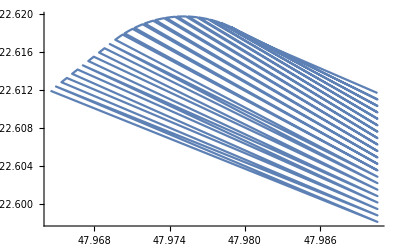

```mathematica
ListLinePlot[crossing//DataProcessor]
```

```mathematica
crossing//DataProcessor//Grid
```

47.9645 | 122.612
47.9906 | 122.598
47.965 | 122.612
47.9906 | 122.599
47.9654 | 122.613
47.9658 | 122.613
47.9906 | 122.6
47.9662 | 122.614
47.9667 | 122.614
47.9906 | 122.6
47.9671 | 122.615
47.9906 | 122.601
47.9675 | 122.615
47.968 | 122.616
47.9906 | 122.602
47.9684 | 122.616
47.9688 | 122.616
47.9906 | 122.602
47.9692 | 122.617
47.9906 | 122.603
47.9697 | 122.617
47.9697 | 122.617
47.9697 | 122.617
47.9698 | 122.617
47.97 | 122.618
47.9701 | 122.618
47.9703 | 122.618
47.9906 | 122.604
47.9704 | 122.618
47.9706 | 122.618
47.9707 | 122.618
47.9709 | 122.618
47.9711 | 122.618
47.9906 | 122.604
47.9712 | 122.619
47.9714 | 122.619
47.9715 | 122.619
47.9717 | 122.619
47.9719 | 122.619
47.9906 | 122.605
47.972 | 122.619
47.9722 | 122.619
47.9724 | 122.619
47.9725 | 122.619
47.9727 | 122.619
47.9906 | 122.606
47.9729 | 122.619
47.973 | 122.619
47.9732 | 122.619
47.9734 | 122.62
47.9736 | 122.62
47.9906 | 122.606
47.9737 | 122.62
47.9739 | 122.62
47.9741 | 122.62
47.9743 | 122.62
47.9744 | 122.62
47.9906 | 122.607
47.9746 | 122.62
47.9748 | 122.62
47.975 | 122.62
47.9751 | 122.62
47.9753 | 122.62
47.9906 | 122.608
47.9755 | 122.62
47.9757 | 122.62
47.9758 | 122.62
47.976 | 122.62
47.9762 | 122.62
47.9906 | 122.608
47.9764 | 122.62
47.9765 | 122.62
47.9767 | 122.62
47.9769 | 122.62
47.9771 | 122.619
47.9906 | 122.609
47.9772 | 122.619
47.9774 | 122.619
47.9776 | 122.619
47.9777 | 122.619
47.9779 | 122.619
47.9906 | 122.61
47.9781 | 122.619
47.9783 | 122.619
47.9784 | 122.619
47.9786 | 122.619
47.9788 | 122.619
47.9906 | 122.61
47.9789 | 122.619
47.9791 | 122.619
47.9792 | 122.618
47.9794 | 122.618
47.9796 | 122.618
47.9906 | 122.611
47.9797 | 122.618
47.9799 | 122.618
47.98 | 122.618
47.9802 | 122.618
47.9803 | 122.618
47.9803 | 122.618
47.9803 | 122.618
47.9906 | 122.612